Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Hadzic2005/./SPHERIC_TestCase12/Flap.datが見付かりませんでした．

Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ren2015/../Hadzic2005Flap_check.datが見付かりませんでした．

Symbol::argx: Symbolは0個の引数で呼ばれました．1つの引数が想定されています．

Part::take: $Failedの2から-1の位置が取れません．

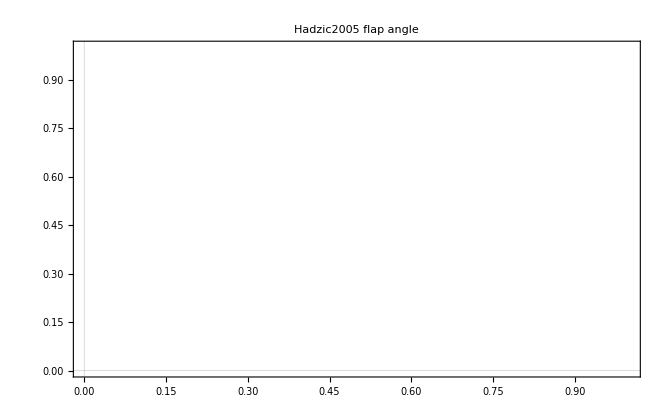

```mathematica
ClearAll["Global`*"];
data=Import[NotebookDirectory[]<>"./SPHERIC_TestCase12/Flap.dat","Data"];
data={#1,#2/180*Pi}&@@@data;
velocity=Import[NotebookDirectory[]<>"../Hadzic2005Flap_check.dat","Data"];
velocity=velocity[[1;;,{1,6}]];
ListPlot[{data[[2;;]],velocity},PlotLabel->"Hadzic2005 flap angle",PlotTheme->"Scientific",Joined->{True,True},PlotRange->{{0,1.},All}]
```

```mathematica
times=data[[2;;,1]];
angles=data[[2;;,2]];

(*Perform Fourier Transform*)
ft=Fourier[angles,FourierParameters->{1,-1}];

(*Compute the frequencies*)
freqs=Range[0,Length[angles]-1]/(Last[times]-First[times]);

(*Only keep the first half of the spectrum*)
half=Ceiling[Length[ft]];
ft=ft[[1;;half]];
freqs=freqs[[1;;half]];

(*Plot the magnitude of the Fourier Transform*)
ListLogPlot[Transpose[{freqs,Abs[ft]}],Joined->True,PlotRange->All]

(*Perform Inverse Fourier Transform*)
reconstructedAngles=InverseFourier[ft,FourierParameters->{1,-1}];

(*Pad the reconstructed data with zeroes to match original data length*)
reconstructedAngles=PadRight[reconstructedAngles,Length[angles]];

(*Compare the original data with the reconstructed data,plotting against time*)
ListLinePlot[{Transpose[{times,angles}],Transpose[{times,Re[reconstructedAngles]}]},PlotLegends->{"Original","Reconstructed"}]
```

Part::take: $Failedの2から-1の位置が取れません．

Fourier::fftl: 引数$Failed⟦2;;All,2⟧は数量の非空のリストでも矩形配列でもありません．

Transpose::nmtx: {{0,1/(1-$Failed)},Abs[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1,-1}]]}の最初の2個のレベルは転置できません．

Fourier::fftl: 引数$Failed⟦2;;All,2⟧は数量の非空のリストでも矩形配列でもありません．

Transpose::nmtx: {{0,1/(1.-1. $Failed)},Abs[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1.,-1.}]]}の最初の2個のレベルは転置できません．

Fourier::fftl: 引数$Failed⟦2;;All,2⟧は数量の非空のリストでも矩形配列でもありません．

Transpose::nmtx: {{0.,1/(1.-1. $Failed)},Abs[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1.,-1.}]]}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Fourier::fftl: 引数$Failed⟦2;;All,2⟧は数量の非空のリストでも矩形配列でもありません．

General::stop: この計算中に，Fourier::fftlのこれ以上の出力は表示されません．

ListLogPlot::lpn: Transpose[{{0.,1/(1.-1. $Failed)},Abs[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1.,-1.}]]}]は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListLogPlot::lpnのこれ以上の出力は表示されません．

ListLogPlot[Transpose[{{0,1/(1-$Failed)},Abs[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1,-1}]]}],Joined→True,PlotRange→All]

InverseFourier::fftl: 引数Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1,-1}]は数量の非空のリストでも矩形配列でもありません．

InverseFourier::nonopt: InverseFourier[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1,-1}],FourierParameters→{1,-1},0]における2の位置より後方にオプションが想定されます（0の代りに）．オプションは規則あるいは規則のリストでなければなりません．

Transpose::nmtx: {$Failed⟦2;;All,1⟧,$Failed⟦2;;All,2⟧}の最初の2個のレベルは転置できません．

Transpose::nmtx: {$Failed⟦2;;All,1⟧,Re[InverseFourier[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1,-1}],FourierParameters→{1,-1},0]]}の最初の2個のレベルは転置できません．

InverseFourier::nonopt: InverseFourier[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1.,-1.}],FourierParameters→{1.,-1.},0]における2の位置より後方にオプションが想定されます（0の代りに）．オプションは規則あるいは規則のリストでなければなりません．

Transpose::nmtx: {$Failed⟦2;;All,1⟧,Re[InverseFourier[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1.,-1.}],FourierParameters→{1.,-1.},0]]}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Fourier::fftl: 引数$Failed⟦2;;All,2⟧は数量の非空のリストでも矩形配列でもありません．

InverseFourier::nonopt: InverseFourier[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1.,-1.}],FourierParameters→{1.,-1.},0.]における2の位置より後方にオプションが想定されます（0.の代りに）．オプションは規則あるいは規則のリストでなければなりません．

Fourier::fftl: 引数$Failed⟦2;;All,2⟧は数量の非空のリストでも矩形配列でもありません．

InverseFourier::nonopt: InverseFourier[Fourier[$Failed⟦2;;All,2⟧,FourierParameters→{1.,-1.}],FourierParameters→{1.,-1.},0.]における2の位置より後方にオプションが想定されます（0.の代りに）．オプションは規則あるいは規則のリストでなければなりません．

General::stop: この計算中に，InverseFourier::nonoptのこれ以上の出力は表示されません．

-Graphics-